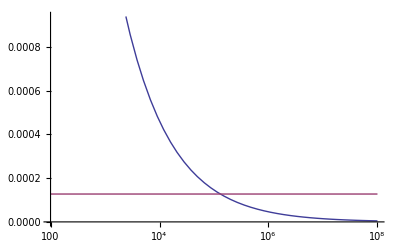

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

Plot::exclul: {4.54339×10^-6\ Im[√ⅇ^Re[« 1 »]\ Abs[BesselI[« 2 »]\ Power[« 2 »]]] - 0, Im[(0.  + 470.58\ ⅈ)\ ⅇ^f] - 0, Im[(0.  + 470.58\ ⅈ)\ ⅇ^f] - 0} must be a list of equalities or real-valued functions.

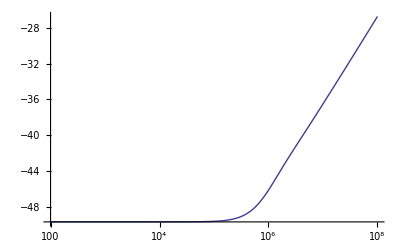

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

Plot::exclul: {Im[√(0.  + 470.58\ ⅈ)\ ⅇ^f\ BesselI[0, 0.0001275\ √Times[« 2 »]]/BesselI[1, 0.0001275\ Power[« 2 »]]] - 0, Im[(0.  + 470.58\ ⅈ)\ ⅇ^f] - 0, Im[(0.  + 470.58\ ⅈ)\ ⅇ^f] - 0, Im[(0.  + 470.58\ ⅈ)\ ⅇ^f] - 0} must be a list of equalities or real-valued functions.

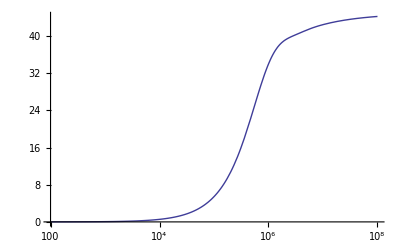

```mathematica
r = .255*10^(-3)/2;
l= .01;
σ = 5.96*10^7;
μ = 1.2566290*10^-6 ;
m = Sqrt[(I*ω*σ*μ)];
LogLinearPlot[{Abs[1/Sqrt[(I*2*Pi*f*σ*μ)]],r},{f,100,100*10^6}]
LogLinearPlot[20*Log[10,Abs[Sqrt[I*2*Pi*f*σ*μ]*l*BesselI[0,Sqrt[I*2*Pi*f*σ*μ]*r]/(2*Pi*r*σ*BesselI[1,Sqrt[I*2*Pi*f*σ*μ]*r])]],{f,100,100*10^6}]
LogLinearPlot[Arg[Sqrt[I*2*Pi*f*σ*μ]*l*BesselI[0,Sqrt[I*2*Pi*f*σ*μ]*r]/(2*Pi*r*σ*BesselI[1,Sqrt[I*2*Pi*f*σ*μ]*r])]/Degree,{f,100,100*10^6}]
```

```mathematica
Export["~/Desktop/radius",%65,"PNG"]
```

~/Desktop/radius

```mathematica
f=10000000
20*Log[10,Abs[Sqrt[I*2*Pi*f*σ*μ]*l*BesselI[0,Sqrt[I*2*Pi*f*σ*μ]*r]/(2*Pi*r*σ*BesselI[1,Sqrt[I*2*Pi*f*σ*μ]*r])]]
```

10000000

-36.5039

```mathematica
(46.1272-26.7414)/2
```

9.6929